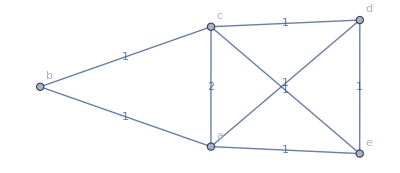

```mathematica
G=Graph[{a,b,c,d,e},{a<->b,a<->e,a<->d,a<->c,b<->c,c<->e,c<->d,d<->e},VertexLabels->Automatic,EdgeWeight->Thread[{a<->b,a<->e,a<->d,a<->c,b<->c,c<->e,c<->d,d<->e}->{1,1,1,2,1,1,1,1}],EdgeLabels->"EdgeWeight"]
```

```mathematica
MultiSet[g_?ConnectedGraphQ]:=Module[{firstToLast,lastToFirst},firstToLast=Graph[Fold[EdgeAdd[#1,DirectedEdge[First[#2],Last[#2]]]&,g,Cases[EdgeList[g],_UndirectedEdge]],EdgeWeight->Join[Values[AssociationMap[AnnotationValue[{g,#},EdgeWeight]&,Cases[EdgeList[g],_UndirectedEdge]]],AnnotationValue[{g,#},EdgeWeight]&/@EdgeList[g]]];lastToFirst=Graph[Fold[EdgeAdd[#1,DirectedEdge[Last[#2],First[#2]]]&,firstToLast,Cases[EdgeList[firstToLast],_UndirectedEdge]],EdgeWeight->Join[Values[AssociationMap[AnnotationValue[{firstToLast,#},EdgeWeight]&,Cases[EdgeList[firstToLast],_UndirectedEdge]]],AnnotationValue[{firstToLast,#},EdgeWeight]&/@EdgeList[firstToLast]]];Graph[Fold[EdgeAdd[#1,UndirectedEdge[Last[#2],First[#2]]]&,lastToFirst,Cases[EdgeList[lastToFirst],_UndirectedEdge]],EdgeWeight->Join[Values[AssociationMap[AnnotationValue[{lastToFirst,#},EdgeWeight]&,Cases[EdgeList[lastToFirst],_UndirectedEdge]]],AnnotationValue[{lastToFirst,#},EdgeWeight]&/@EdgeList[lastToFirst]],EdgeCapacity->Join[ConstantArray[∞,3EdgeCount[g]],ConstantArray[2,EdgeCount[g]]]]]
```

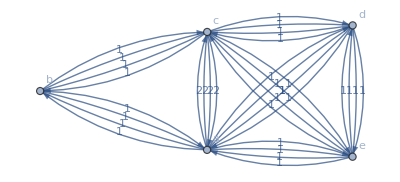

```mathematica
MultiSet[G]
```

```mathematica
FindMinimumCostFlow[MultiSet[G],{1,1,1,1,1}]
```

FindMinimumCostFlow[-Graphics-,{1,1,1,1,1}]

```mathematica
(VertexInDegree[G,#]-VertexOutDegree[G,#])&/@VertexList[G]
```

{0,0,0,0,0}

```mathematica
RandomWeightedGraphTriangleInequality[vertices_,threshhold_]:=First@TakeLargestBy[ConnectedGraphComponents@Module[{randomGraph},randomGraph=RandomGraph[SpatialGraphDistribution[vertices,threshhold]];Graph[randomGraph,EdgeWeight->Thread[EdgeList[randomGraph]->(EuclideanDistance[AnnotationValue[{randomGraph,First[#]},VertexCoordinates],AnnotationValue[{randomGraph,Last[#]},VertexCoordinates]]&/@EdgeList[randomGraph])],EdgeLabels->"EdgeWeight",ImageSize->Full]],EdgeCount,1]
```

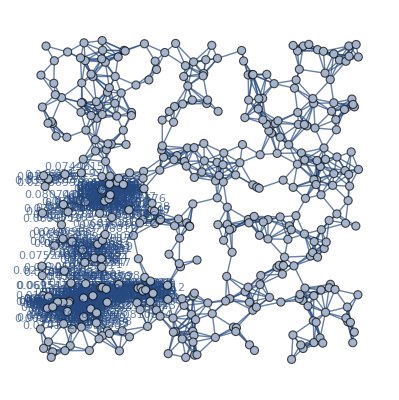

```mathematica
RandomWeightedGraphTriangleInequality[403,ⅇ^-2.5]
```

```mathematica
MixedGraph[g_,threshold_]:=Block[{replaceCount},replaceCount=Floor[threshold EdgeCount[g]];Graph[Fold[EdgeAdd[EdgeDelete[#1,#2],First[#2]->Last[#2]]&,g,RandomSample[EdgeList[g],replaceCount]],EdgeWeight->Thread[EdgeList[g]->(AnnotationValue[{g,#},EdgeWeight]&/@EdgeList[g])]]]
```

```mathematica
MixedGraph[G,.4]//InputForm
```

Graph[{a, b, c, d, e}, {UndirectedEdge[a, b], UndirectedEdge[a, e], UndirectedEdge[a, c], UndirectedEdge[c, e], UndirectedEdge[c, d], 
  DirectedEdge[b, c], DirectedEdge[a, d], DirectedEdge[d, e]}, {EdgeLabels -> {"EdgeWeight"}, EdgeWeight -> {1, 1, 2, 1, 1, 1, 1, 1}, 
  GraphLayout -> {"Dimension" -> 2}, VertexLabels -> {Automatic}}]

## FindMinimumCostFlow

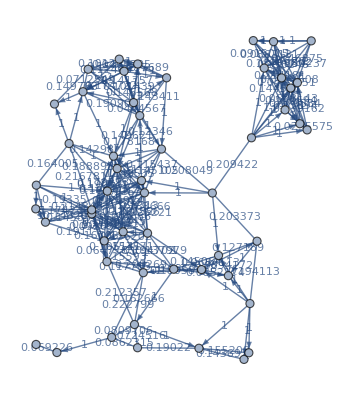

```mathematica
R=Graph[MixedGraph[RandomWeightedGraphTriangleInequality[54,ⅇ^-1.5],0.5]]
```

```mathematica
(VertexInDegree[R,#]-VertexOutDegree[R,#])&/@VertexList[R]
```

{-4,3,8,2,-3,2,1,3,-1,3,-4,-5,4,-4,-3,-1,3,-3,0,-6,2,-3,1,3,2,0,-1,2,3,0,2,-1,-3,4,-3,-7,0,-6,1,0,2,-3,2,1,3,3,0,6,0,-1,-4,0}

```mathematica
FindMinimumCostFlow[R,(VertexInDegree[R,#]-VertexOutDegree[R,#])&/@VertexList[R]]
```

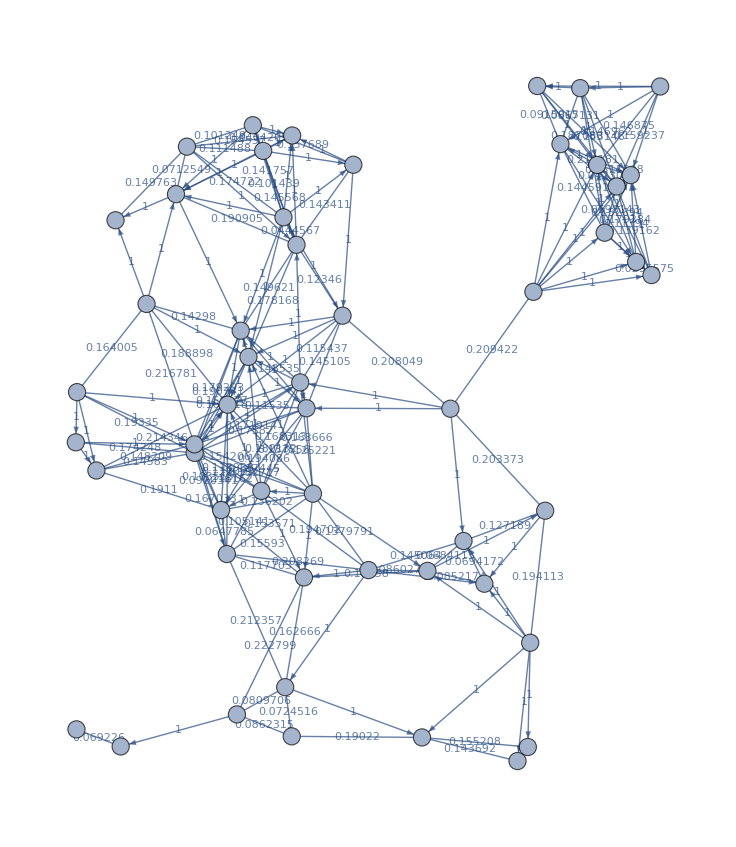
```mathematica
FindMinimumCostFlow[-Graphics-,{-4,3,8,2,-3,2,1,3,-1,3,-4,-5,4,-4,-3,-1,3,-3,0,-6,2,-3,1,3,2,0,-1,2,3,0,2,-1,-3,4,-3,-7,0,-6,1,0,2,-3,2,1,3,3,0,6,0,-1,-4,0}]
```

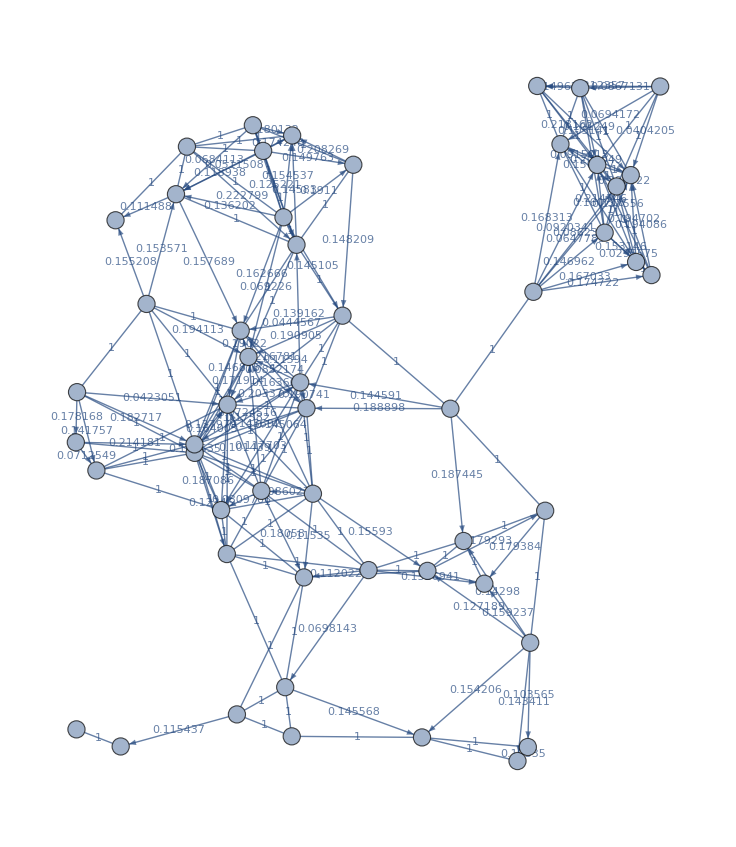
FindMinimumCostFlow[-Graphics-,{-4,3,8,2,-3,2,1,3,-1,3,-4,-5,4,-4,-3,-1,3,-3,0,-6,2,-3,1,3,2,0,-1,2,3,0,2,-1,-3,4,-3,-7,0,-6,1,0,2,-3,2,1,3,3,0,6,0,-1,-4,0}]